```mathematica
ClearAll["Global`*"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
(*We compare the results of <ϵ> vs Subscript[θ, c] and those of σ vs Subscript[θ, c]*)
```

```mathematica
(*Collecting Data and Pre-processing*)
```

InterpolatingFunction[…]

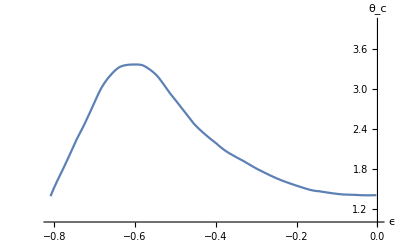

InterpolatingFunction[…]

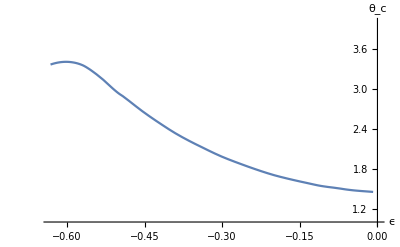

InterpolatingFunction[…]

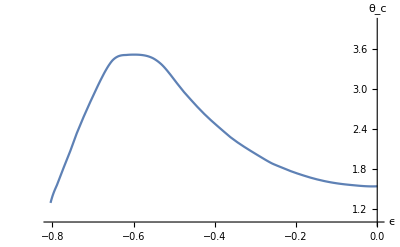

```mathematica
(*Experiment 1. 
The 1 2 3 correspond to different samples.
-Graphics-*)
ϵvsTc1:={{-0.0027881040892192566,1.4042553191489362},{-0.044052044609665275,1.4042553191489362},{-0.06412639405204457,1.4095744680851063},{-0.08643122676579928,1.414893617021277},{-0.10315985130111516,1.4255319148936172},{-0.1444237918215613,1.4627659574468086},{-0.1667286245353159,1.4840425531914896},{-0.18457249070631965,1.5159574468085109},{-0.20353159851301106,1.5531914893617023},{-0.2213754646840148,1.5904255319148937},{-0.24033457249070622,1.6329787234042552},{-0.2604089219330854,1.6861702127659575},{-0.2838289962825278,1.7553191489361704},{-0.3061338289962825,1.824468085106383},{-0.32620817843866157,1.898936170212766},{-0.3618959107806691,2.015957446808511},{-0.39758364312267647,2.175531914893617},{-0.4544609665427508,2.4787234042553195},{-0.5001858736059479,2.835106382978723},{-0.5236059479553903,3.0212765957446805},{-0.5436802973977695,3.1861702127659575},{-0.5648698884758363,3.2978723404255317},{-0.5815985130111523,3.356382978723404},{-0.6005576208178438,3.367021276595745},{-0.6184014869888474,3.361702127659574},{-0.6395910780669143,3.324468085106383},{-0.6596654275092935,3.2127659574468086},{-0.6842007434944237,3.00531914893617},{-0.7042750929368029,2.74468085106383},{-0.7243494423791821,2.4787234042553195},{-0.7477695167286245,2.2021276595744683},{-0.7678438661710036,1.9255319148936172},{-0.7901486988847581,1.648936170212766},{-0.8091078066914497,1.3882978723404258}}
Tc1=Range[Length[ϵvsTc1]];
ϵ1=Range[Length[ϵvsTc1]];
For[i=1,i<=Length[ϵvsTc1],i++,Tc1[[i]]=ϵvsTc1[[i]][[2]];ϵ1[[i]]=ϵvsTc1[[i]][[1]]]
{Length[Tc1],Length[ϵ1]};
Tc1;
ϵ1;
θc1=Interpolation[ϵvsTc1](*Gives me θ_c(ϵ)*)
Plot[θc1[x],{x,ϵ1[[Length[ϵ1]]],ϵ1[[1]]},AxesLabel->{ϵ,Subscript[θ, c]},PlotRange->{1,4}]
ϵvsTc2:={{-0.00836431226765788,1.4521276595744683},{-0.026208178438661633,1.4627659574468086},{-0.04293680297397773,1.4734042553191489},{-0.06078066914498126,1.4893617021276597},{-0.07862453531598501,1.5106382978723407},{-0.095353159851301,1.5265957446808511},{-0.11319702602230475,1.5478723404255321},{-0.13215613382899616,1.5797872340425534},{-0.15111524163568768,1.6117021276595747},{-0.16895910780669143,1.643617021276596},{-0.20130111524163563,1.7074468085106385},{-0.2314126394052043,1.7819148936170215},{-0.26598513011152414,1.877659574468085},{-0.3027881040892192,1.9893617021276597},{-0.3373605947955389,2.117021276595745},{-0.3964684014869887,2.3617021276595747},{-0.416542750929368,2.4627659574468086},{-0.45334572490706304,2.6595744680851063},{-0.4901486988847582,2.882978723404255},{-0.520260223048327,3.0691489361702127},{-0.5291821561338289,3.132978723404255},{-0.5481412639405203,3.25},{-0.5682156133828995,3.351063829787234},{-0.5882899628252787,3.3989361702127656},{-0.6105947955390333,3.404255319148936},{-0.6317843866171002,3.367021276595745}}
Tc2=Range[Length[ϵvsTc2]];
ϵ2=Range[Length[ϵvsTc2]];
For[i=1,i<=Length[ϵvsTc2],i++,Tc2[[i]]=ϵvsTc2[[i]][[2]];ϵ2[[i]]=ϵvsTc2[[i]][[1]]]
{Length[Tc2],Length[ϵ2]};
Tc2;
ϵ2;
θc2=Interpolation[ϵvsTc2](*Gives me θ_c(ϵ)*)
Plot[θc2[x],{x,ϵ2[[Length[ϵ2]]],ϵ2[[1]]},AxesLabel->{ϵ,Subscript[θ, c]},PlotRange->{1,4}]
ϵvsTc3:={{0.0005576208178438291,1.5372340425531914},{-0.025092936802973864,1.5372340425531914},{-0.05855018587360594,1.5531914893617023},{-0.08420074349442375,1.5691489361702131},{-0.10873605947955378,1.5904255319148937},{-0.13550185873605936,1.622340425531915},{-0.1600371747211895,1.6595744680851063},{-0.1856877323420073,1.7074468085106385},{-0.21133828996282522,1.7606382978723405},{-0.23698884758364303,1.824468085106383},{-0.25817843866171,1.877659574468085},{-0.287174721189591,1.9787234042553192},{-0.3117100371747211,2.0691489361702127},{-0.33624535315985127,2.1648936170212765},{-0.3607806691449813,2.271276595744681},{-0.3830855018587359,2.3882978723404253},{-0.41096654275092925,2.5372340425531914},{-0.43438661710037163,2.675531914893617},{-0.457806691449814,2.829787234042553},{-0.48234200743494404,3},{-0.5057620817843865,3.1861702127659575},{-0.5291821561338289,3.356382978723404},{-0.5526022304832712,3.4627659574468086},{-0.5804832713754646,3.5106382978723403},{-0.5983271375464683,3.5159574468085104},{-0.6184014869888474,3.5106382978723403},{-0.6384758364312266,3.4893617021276593},{-0.6518587360594794,3.4308510638297873},{-0.6674721189591077,3.2925531914893615},{-0.683085501858736,3.1117021276595747},{-0.6975836431226765,2.925531914893617},{-0.712081784386617,2.7340425531914896},{-0.7265799256505574,2.5319148936170213},{-0.7399628252788102,2.3351063829787235},{-0.7522304832713753,2.127659574468085},{-0.7644981412639403,1.9361702127659575},{-0.7767657992565055,1.7500000000000002},{-0.7890334572490705,1.5531914893617023},{-0.8001858736059477,1.3829787234042556},{-0.8046468401486988,1.2872340425531914}}
Tc3=Range[Length[ϵvsTc3]];
ϵ3=Range[Length[ϵvsTc3]];
For[i=1,i<=Length[ϵvsTc3],i++,Tc3[[i]]=ϵvsTc3[[i]][[2]];ϵ3[[i]]=ϵvsTc3[[i]][[1]]]
{Length[Tc3],Length[ϵ3]};
Tc3;
ϵ3;
θc3=Interpolation[ϵvsTc3](*Gives me θ_c(ϵ)*)
Plot[θc3[x],{x,ϵ3[[Length[ϵ3]]],ϵ3[[1]]},AxesLabel->{ϵ,Subscript[θ, c]},PlotRange->{1,4}]
```

InterpolatingFunction[…]

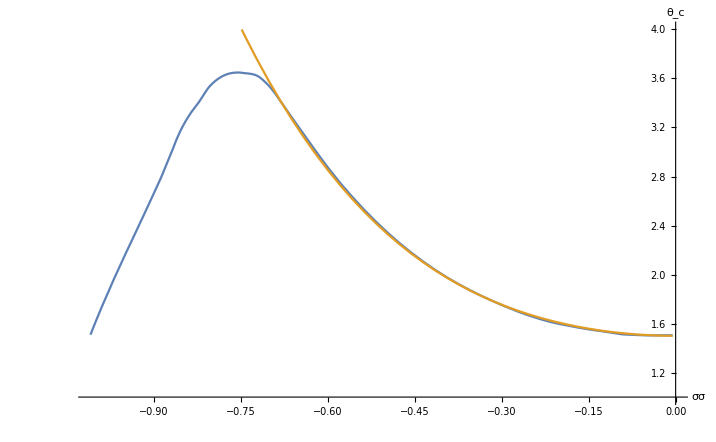

Plot::plln: Limiting value List in {x,List,0} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[{5 Abs[x]+14 Abs[x]^3},{x,σstar⟦Length[σstar]⟧,0}]].

Show[-Graphics-,Plot[{5 Abs[x]+14 Abs[x]^3},{x,σstar⟦Length[σstar]⟧,0}]]

```mathematica
(*Experiment 2. 
We plot the Stress vs Transition Temperature curve
-Graphics-*)
σvsTc4:={{-0.005244338498212375,1.5038230597971527},{-0.030989272943981128,1.5037331054489842},{-0.04958283671036967,1.5036681384197519},{-0.07246722288438634,1.5077810511165581},{-0.09106078665077488,1.511908956204726},{-0.11966626936829572,1.5327733675159858},{-0.1396901072705603,1.5452820193751666},{-0.18545887961859364,1.5828579495905823},{-0.2112038140643624,1.6079252279468168},{-0.2755661501787844,1.7041364007766058},{-0.30131108462455314,1.7543609118372423},{-0.3928486293206199,1.972070424259688},{-0.4815256257449346,2.277840246075117},{-0.5702026221692492,2.7010104871777574},{-0.6588796185935638,3.2625455081546115},{-0.6789034564958284,3.396647451418405},{-0.698927294398093,3.5265565225647983},{-0.7103694874851014,3.5810238803807066},{-0.7189511323003577,3.6145368725371876},{-0.730393325387366,3.6354612534138924},{-0.7504171632896306,3.647969905273074},{-0.7733015494636473,3.635311329500279},{-0.7833134684147796,3.614311986666767},{-0.7947556615017879,3.576536157899866},{-0.8061978545887962,3.5219888406633633},{-0.8162097735399285,3.4506750324210462},{-0.8290822407628129,3.366772612898954},{-0.8734207389749702,2.9347518634293097},{-0.9191895113230035,2.4649902674392745},{-0.9649582836710369,2.0036144156840403},{-1.0092967818831942,1.5087005844533903}}
Tc4=Range[Length[σvsTc4]];
σ4=Range[Length[σvsTc4]];
For[i=1,i<=Length[σvsTc4],i++,Tc4[[i]]=σvsTc4[[i]][[2]];σ4[[i]]=σvsTc4[[i]][[1]]]
{Length[Tc4],Length[σ4]};
Tc4;
σ4;
θc4=Interpolation[σvsTc4](*Gives me θ_c(σ)*)
Plot[{θc4[x],1.5+2.5*x^2+3.5*x^4},{x,σ4[[Length[σ4]]],σ4[[1]]},AxesLabel->{σσ,Subscript[θ, c]},PlotRange->{1,4}]
dtbds=Range[Length[σ]-1];  (*dθ/dσ*)
σstar=Range[Length[σ]-1];(*θ^* corresponding to the y coordinate of the point which has the same slope as the discrete slope calculated above.*)
For[i=1,i<=Length[σ]-1,i++,dtbds[[i]]=(Tc4[[i+1]]-Tc4[[i]])/(σ4[[i+1]]-σ4[[i]]);σstar[[i]]=(σ4[[i+1]]+σ4[[i]])/2]
pltσ2 =ListPlot[Transpose@{σstar,-dtbds},AxesLabel->Automatic];(*Transition temp Subscript[θ, c] vs Subscript[dθ, c]/dσ. We have also changed the compression to tension by plotting -Subscript[dθ, c]/dσ = Subscript[dθ, c]/d(-σ). It also makes it easier to see.*)
pltσ2a = Plot[{5*Abs[x]+14*Abs[x]^3},{x,σstar[[Length[σstar]]],0}];
Show[pltσ2,pltσ2a]
```

```mathematica
(*Inverting the Functions*)
σ4max:=σ4[[Position[Tc4,Max[Tc4]][[1]][[1]]]];
ϵ1max=ϵ1[[Position[Tc1,Max[Tc1]][[1]][[1]]]];
ϵ2max=ϵ2[[Position[Tc2,Max[Tc2]][[1]][[1]]]];
ϵ3max=ϵ3[[Position[Tc3,Max[Tc3]][[1]][[1]]]];
{Max[Tc1],Position[Tc1,Max[Tc1]][[1]][[1]],ϵ1[[Position[Tc1,Max[Tc1]][[1]][[1]]]],θc1[ϵ1[[Position[Tc1,Max[Tc1]][[1]][[1]]]]]};(*Testing the menthod ot extract the value of ϵ corresponding to max θc.*)
(*In order to invert the above functions from θ(ϵ) to ϵ(θ), owing to the multi valuedness of the inverse, we create two separate inverses, one to the left of ϵ#max (# is 1,2or3) and one to its right. The functions will be called θcR# and θcL# .
In order to restrict the function to the left half, we have had to make it monotonic on the interval (0,ϵ1max), this means extending it in this region with a straingt line. If we choose the value at ϵ=0 to be Max[Tc1]+δ, thewn the equation of the line is
θc=max(Tc#)+δ/-ϵ1max*(ϵ-ϵ1max)
The parameter δ is defined below.
Apparently this is enough to plot the inverse, the striaght line used to make the function monotonic doesnt's show up anywhere except for the case of Sample 2 (Experiment 1).
*)
δ:=0.01
θcR1[x_]:=Piecewise[{{0,x<ϵ1max},{θc1[x],ϵ1max<x<0}}];
θcL1[x_]:=Piecewise[{{θc1[x],x<ϵ1max},{Max[Tc1]+δ/-ϵ1max*(x-ϵ1max),ϵ1max<=x}}];
(*,*)
θcR2[x_]:=Piecewise[{{0,x<ϵ2max},{θc2[x],ϵ2max<x<0}}];
θcL2[x_]:=Piecewise[{{θc2[x],x<ϵ2max},{Max[Tc2]+δ/-ϵ2max*(x-ϵ2max),ϵ2max<x}}];
θcR3[x_]:=Piecewise[{{0,x<ϵ3max},{θc3[x],ϵ3max<x<0}}];
θcL3[x_]:=Piecewise[{{θc3[x],x<ϵ3max},{Max[Tc3]+δ/-ϵ3max*(x-ϵ3max),ϵ3max<x}}];
θcR4[x_]:=Piecewise[{{0,x<σ4max},{θc4[x],σ4max<x<0}}];
θcL4[x_]:=Piecewise[{{θc4[x],x<σ4max},{Max[Tc4]+δ/-σ4max*(x-σ4max),σ4max<x}}];
(*In the following, we plot the above defined functions. We plot θc# with a vertical shift to distinguish it from the others.*)
Plot[{θcR1[x],θcL1[x],θc1[x]+0.1},{x,ϵ1[[Length[ϵ1]]],ϵ1[[1]]}];
Plot[{θcR2[x],θcL2[x],θc2[x]+0.1},{x,ϵ2[[Length[ϵ2]]],ϵ2[[1]]}];
Plot[{θcR3[x],θcL3[x],θc3[x]+0.1},{x,ϵ3[[Length[ϵ3]]],ϵ3[[1]]}];
Plot[{θcR4[x],θcL4[x],θc4[x]+0.1},{x,σ4[[Length[σ4]]],σ4[[1]]}];
(*We now Define the Inverse of these functions. The function is now ϵ_c(θ) or σ_c(θ)*)
ϵc1R[x_]:=InverseFunction[θcR1][x]
ϵc1L[x_]:=InverseFunction[θcL1][x]
ϵc2R[x_]:=InverseFunction[θcR2][x]
ϵc2L[x_]:=InverseFunction[θcL2][x]
ϵc3R[x_]:=InverseFunction[θcR3][x]
ϵc3L[x_]:=InverseFunction[θcL3][x]
σc4R[x_]:=InverseFunction[θcR4][x]
σc4L[x_]:=InverseFunction[θcL4][x]
Plot[{θcL1[x],θcR1[x]},{x,ϵ1[[Length[ϵ1]]],ϵ1[[1]]},AxesLabel->{Subscript[ϵ, 1],Subscript[θc, 1]},PlotLabels->{"θcL1","θcR1"}]
Plot[{-ϵc1L[x],-ϵc1R[x]},{x,Tc1[[1]],Max[Tc1]},AxesLabel->{θc,Subscript[ϵ, 1]},PlotLabels->{"ϵc1L","ϵc1R"}]
Plot[{θcL2[x],θcR2[x]},{x,ϵ2[[Length[ϵ2]]],ϵ2[[1]]},PlotLabels->{"θcL2","θcR2"}];
Plot[{-ϵc2L[x],-ϵc2R[x]},{x,Tc2[[1]],Max[Tc2]},PlotLabels->{"ϵc12L","ϵc2R"}];
Plot[{θcL3[x],θcR3[x]},{x,ϵ3[[Length[ϵ3]]],ϵ3[[1]]},PlotLabels->{"θcL3","θcR3"}];
Plot[{-ϵc3L[x],-ϵc3R[x]},{x,Tc3[[1]],Max[Tc3]},PlotLabels->{"ϵc3L","ϵc3R"}];
Plot[{θcL4[x],θcR4[x]},{x,σ4[[Length[σ4]]],σ4[[1]]},PlotLabels->{"θcL4","θcR4"}]
Plot[{-σc4L[x],-σc4R[x]},{x,Tc4[[1]],Max[Tc4]},PlotLabels->{"σc4L","σc4R"}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

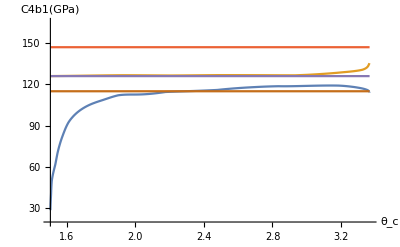

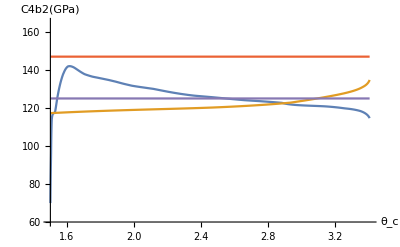

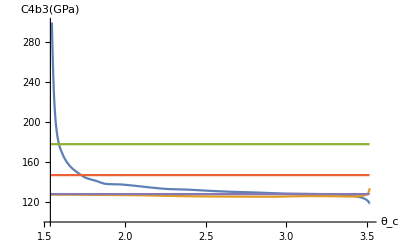

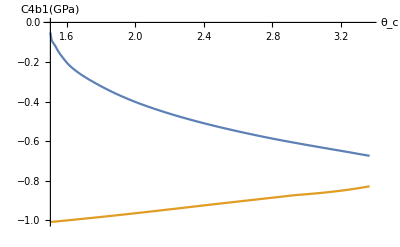

```mathematica
(*Plotting the Ratios (σ(Subscript[θ, c]))/(ϵ(Subscript[θ, c]))*)
(*We first note that We are trying to plot σ/ϵ at the Transition temperature to get an idea of the Elastic modulus. Whether the two have the same dependence on the Transition temperature. We have also plotted σ/ϵ(Subscript[θ, c]) from above and below, these correspond to the values 178 GPa and 147 GPa. For each we have drawn some approximate lines that closely approximate (σ(Subscript[θ, c]))/(ϵ(Subscript[θ, c]))*)
Plot[{σc4R[x]/ϵc1R[x]*100,100*σc4L[x]/ϵc1L[x],178,147,126,115},{x,Max[Tc1[[1]],Tc4[[1]]],Min[Max[Tc1],Max[Tc4]]},AxesLabel->{Subscript[θ, c],C4b1 [GPa]},PlotRange->{0.2*100,100*1.65}](*Here 125*)
Plot[{σc4R[x]/ϵc2R[x]*100,100*σc4L[x]/ϵc2L[x],178,147,125},{x,Max[Tc2[[1]],Tc4[[1]]],Min[Max[Tc2],Max[Tc4]]},AxesLabel->{Subscript[θ, c],C4b2 [GPa]},PlotRange->{0.6*100,100*1.65}]
Plot[{σc4R[x]/ϵc3R[x]*100,100*σc4L[x]/ϵc3L[x],178,147,128},{x,Max[Tc3[[1]],Tc4[[1]]],Min[Max[Tc3],Max[Tc4]]},AxesLabel->{Subscript[θ, c],C4b3 [GPa]},PlotRange->{1*100,100*3}]
Plot[{σc4R[x],σc4L[x]},{x,Max[Tc1[[1]],Tc4[[1]]],Min[Max[Tc1],Max[Tc4]]},AxesLabel->{Subscript[θ, c],C4b1 [GPa]}](*Here 125*)
```

1.

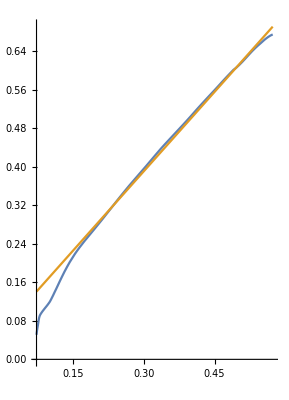

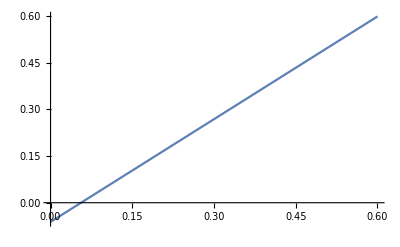

```mathematica
(*Testing out Different theories*)
(*Using the lambda from dp/Subscript[dθ, c] to match with dσ/Subscript[dθ, c] allowing for the touching point to change.*)
(*Theory
We have the following for a pressure + dead load applied simeltaneously.
dp/dθ(Subscript[v, S]-Subscript[v, N])-dσ/dθ(Subscript[ϵ, S]-Subscript[ϵ, N])=Subscript[η, S]-Subscript[η, N]
Applying them separately and equating the two, we get
dp/dθ(Subscript[v, S]-Subscript[v, N])=Subscript[η, S]-Subscript[η, N]=dσ/dθ(Subscript[ϵ, N]-Subscript[ϵ, S])
35.2*10^8*(V-1)=10^6/(5σ+14 σ^3)(Subscript[ϵ, S]-0)
Note that the plot of 5σ+14*σ^2=dθ/dσ has been verified above.
where in the above we have substituted the expression for dp/dθ and dσ/dθ along with the fact that in the normal state vN~1 and ϵN~0. We can aslo use the fact that epsilon is measured in percentage, ergo the 100 multiplying
35.2*(5σ+14 σ^3)*10^4*(Subscript[v, S]-1)=Subscript[ϵ, S] (in %)
Now we know that ϵ_S is in the range of 0,0.6, which means that we can use this to find an upperbound for Subscript[v, S]
Subscript[v, S,max]=1+0.6/(0.76*(5+14*0.76^2)*35.2*10^4)=1+1.7138578726824622*10^-7
where we have substituted the maximum vlaue of σ_max as 0.76 based on the curve above under the heading " (*Experiment\ 2. \ We\ plot\ the\ Stress\ vs\ Transition\ Temperature\ curve*) "
*)
Subscript[v, S,max]=1+0.6/(0.76*(5+14*0.76^2)*35.2*10^4)
(*Manipulate[Plot[{V*35.2*10^4*x*(5+14*x^2),},{x,0,0.6}],{V,0,Subscript[v, S,max]-1}]*)
(*Plot[{σc4R[x]/ϵc3R[x],1.3},{x,Max[Tc1[[1]],Tc4[[1]]],Min[Max[Tc1],Max[Tc4]]},AxesLabel->{Subscript[θ, c],C4b1 [GPa]},PlotRange->{0.2,10}](*Trying ot get an estimate of Subscript[σ, c] vs Subscript[ϵ, c]*)*)
ParametricPlot[{{-ϵc2R[x],-σc4R[x]},{-ϵc2R[x],-1.1*(ϵc2R[x]-0.055)}},{x,Max[Tc1[[1]],Tc4[[1]]],Min[Max[Tc1],Max[Tc4]]}](*Plotting the above parametrically*)
σC[x_]:=1.1*(x-0.056)(*parametric definition of σ vs <ϵ> based on the interpolation above.*)
Manipulate[Plot[{0.056,0.056+V*35.2*10^4*σC[x]*(5+14*σC[x]^2),0.6,x},{x,0.056,0.6}],{V,0,Subscript[v, S,max]-1}]
(*In the above we are checking if Subscript[ϵ, N]~0.056< Subscript[ϵ, c] < Subscript[ϵ, S](Subscript[ϵ, c]) < Subscript[ϵ, s,max]=0.6
where Subscript[ϵ, c] is the average epsilon
The first inequality is satisfies as the curve Subscript[ϵ, S](Subscript[ϵ, c]) lies above Subscript[ϵ, N]. The last one is satisfies as Subscript[ϵ, S](Subscript[ϵ, c])<Subscript[ϵ, s,max]=0.6. However,   Subscript[ϵ, S](Subscript[ϵ, c])< Subscript[ϵ, c] where Subscript[ϵ, c] is  the y=x line since its what we are plotting agianst. Hence the average strain is greater than the SC strain. Which is a contradiction.
*)
Plot[σC[x],{x,0,0.60}]
```

```mathematica
(*Equivalent Elastic modulus for σ/ϵ*)
 (*We write doen the expression for the effective elastic modulus along the x direction. This corresponds to applying a stress Subscript[σ, xx] and computing Subscript[ϵ, xx] to get Subscript[C, xx] the equivalent stress*)
Cc={{c11,c12,c13,0,0,0},{c12,c11,c13,0,0,0},{c13,c13,c33,0,0,0},{0,0,0,c44,0,0},{0,0,0,0,c44,0},{0,0,0,0,0,c66}};(*Elastic Modulus with Tertragonal Symmetry*)
Sxx=MatrixForm[Inverse[Cc].Transpose[{1,0,0,0,0,0}]];(*Solve for Strains for unit stress along the x direction. This we can use to define an effective Compliance Modulus*)
Sxx[[1]][[1]]
(*Using the output of the above, we define a function which describes the equivalent Elastic Modulus along for xx. We set it as the inverse of the compliance*)
Ceq[x11_,x12_,x13_,x33_,x44_,x66_]:=(-2*x11*x13^2*x44^2*x66+2*x12*x13^2*x44^2*x66+x11^2*x33*x44^2*x66-x12^2*x33*x44^2*x66)/(-x13^2* x44^2*x66+x11*x33*x44^2*x66) 
Ceq[x11,x12,x13,x33,x44,x66]
```

(-c13^2 c44^2 c66+c11 c33 c44^2 c66)/(-2 c11 c13^2 c44^2 c66+2 c12 c13^2 c44^2 c66+c11^2 c33 c44^2 c66-c12^2 c33 c44^2 c66)

(-2 x11 x13^2 x44^2 x66+2 x12 x13^2 x44^2 x66+x11^2 x33 x44^2 x66-x12^2 x33 x44^2 x66)/(-x13^2 x44^2 x66+x11 x33 x44^2 x66)

Cequiv from above is 178.011.

Cequiv from below is 147.601.

C11 from above is 243.409.

C11 from below is 152.287.

C12 from above is 117.813.

C12 from below is 26.6906.

C13 from above is 88.6826.

C13 from below is 1.49874.

C33 from above is 282.337.

C33 from below is 191.118.

C44 from above is 72.7862.

C44 from below is 69.9394.

C66 from above is 69.1107.

C66 from below is 58.8297.

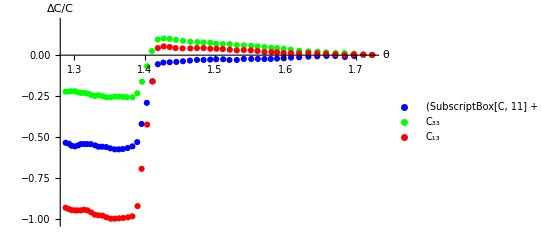

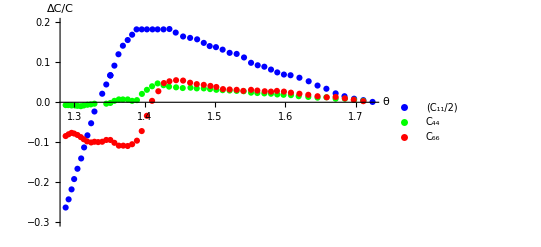

```mathematica
(*Computing the Jump in C*)
 (*Here we shall compute the Value of C and the corresponding Jumps. We use the data from Books/superconductivity/papers/Effect of Stress on Tc/"jump in elastic modulus of Sr2RuO4". The images correspond to 
-Graphics--Graphics-

Notice that the reference for the Graphs is taken at 1.7K. We know the values at 4K; that is what is reported in the paper. We will use the value at 4K as the value at 1.7K
*)
Subscript[c11pc12b2, 0]=190.8; (*(Subscript[C, 11]+Subscript[C, 12])/2 at 4K ~at 1.7K in GPa*)
Subscript[c33, 0]=257.2;(*Subscript[c, 33] at 4K ~at 1.7K in GPa*)
Subscript[c13, 0]=85;(*Subscript[c, 13] at 4K ~at 1.7K in GPa*)
Subscript[c11mc12b2, 0]=53.1; (*(Subscript[C, 11]-Subscript[C, 12])/2 at 4K ~at 1.7K in GPa*)
Subscript[c44, 0]=69.5;(*Subscript[c, 44] at 4K ~at 1.7K in GPa*)
Subscript[c66, 0]=65.6;(*Subscript[c, 66] at 4K ~at 1.7K in GPa*)
(*The values at the Transition temperature, form both above and below.*)
C11p12b2plus=Subscript[c11pc12b2, 0]*(1-0.05340050377833758) ;(*The 'plus' stands for a limit from above*)
C11p12b2minus=Subscript[c11pc12b2, 0]*(1-0.5309823677581865);(*The 'minus' stands for a limit from below*)
C33plus=Subscript[c33, 0]*(1+0.09773299748110824); (*The 'plus' stands for a limit from above*)
C33minus=Subscript[c33, 0]*(1-0.25692695214105804);(*The 'minus' stands for a limit from below*)
C13plus=Subscript[c13, 0]*(1+0.04332493702770776); (*The 'plus' stands for a limit from above*)
C13minus=Subscript[c13, 0]*(1-0.9823677581863984);(*The 'minus' stands for a limit from below*)
C11m12b2plus=Subscript[c11mc12b2, 0]*(1+0.18263579697239543) ;(*The 'plus' stands for a limit from above*)
C11m12b2minus=Subscript[c11mc12b2, 0]*(1+0.18263579697239543);(*The 'minus' stands for a limit from below*)
C44plus=Subscript[c44, 0]*(1+0.04728406055209264) ;(*The 'plus' stands for a limit from above*)
C44minus=Subscript[c44, 0]*(1+0.006322350845948399);(*The 'minus' stands for a limit from below*)
C66plus=Subscript[c66, 0]*(1+0.05351736420302766); (*The 'plus' stands for a limit from above*)
C66minus=Subscript[c66, 0]*(1-0.10320569902048088);(*The 'minus' stands for a limit from below*)
C11plus=C11p12b2plus+C11m12b2plus;
C11minus=C11p12b2minus+C11m12b2minus;
C12plus=C11p12b2plus-C11m12b2plus;
C12minus=C11p12b2minus-C11m12b2minus;
(*Evaluating the Equivalent Elastic Modulus at the Transition temperature*)
StringForm["Cequiv from above is ``.",Ceq[C11plus,C12plus,C13plus,C33plus,C44plus,C66plus]]
StringForm["Cequiv from below is ``.",Ceq[C11minus,C12minus,C13minus,C33minus,C44minus,C66minus]]
StringForm["C11 from above is ``.",C11plus]
StringForm["C11 from below is ``.",C11minus]
StringForm["C12 from above is ``.",C12plus]
StringForm["C12 from below is ``.",C12minus]
StringForm["C13 from above is ``.",C13plus]
StringForm["C13 from below is ``.",C13minus]
StringForm["C33 from above is ``.",C33plus]
StringForm["C33 from below is ``.",C33minus]
StringForm["C44 from above is ``.",C44plus]
StringForm["C44 from below is ``.",C44minus]
StringForm["C66 from above is ``.",C66plus]
StringForm["C66 from below is ``.",C66minus]

(*We write down the functional dependence of the data*)
c11pc12b2vsT={{1.7233289646133683,0.0010084033613446397},{1.7107470511140237,0.0010084033613446397},{1.697640891218873,-0.005042016806722588},{1.6845347313237222,-0.011092436974789788},{1.6709043250327653,-0.005042016806722588},{1.6583224115334207,-0.005042016806722588},{1.64521625163827,-0.007058823529411645},{1.6326343381389254,-0.00907563025210073},{1.6195281782437747,-0.013109243697478873},{1.607994757536042,-0.015126050420167958},{1.5975098296199215,-0.0191596638655461},{1.5880733944954128,-0.021176470588235158},{1.5791612057667104,-0.02319327731092427},{1.570249017038008,-0.02319327731092427},{1.5608125819134995,-0.02319327731092427},{1.5513761467889908,-0.02319327731092427},{1.5408912188728703,-0.02319327731092427},{1.5309305373525557,-0.02924369747899147},{1.5204456094364351,-0.02924369747899147},{1.5115334207077327,-0.025210084033613328},{1.501572739187418,-0.025210084033613328},{1.4931847968545218,-0.027226890756302413},{1.4837483617300131,-0.02924369747899147},{1.4743119266055047,-0.02924369747899147},{1.46435124508519,-0.03327731092436964},{1.4543905635648755,-0.03731092436974778},{1.444954128440367,-0.041344537815125953},{1.4355176933158584,-0.04336134453781501},{1.426605504587156,-0.04537815126050407},{1.4187418086500656,-0.05546218487394944},{1.4108781127129753,-0.16033613445378142},{1.4030144167758847,-0.2914285714285713},{1.3956749672346003,-0.42050420168067215},{1.389384010484928,-0.5314285714285715},{1.3825688073394495,-0.5576470588235294},{1.3757536041939713,-0.5677310924369748},{1.3689384010484928,-0.5737815126050421},{1.3631716906946265,-0.5757983193277311},{1.3574049803407602,-0.5757983193277311},{1.351114023591088,-0.5697478991596638},{1.3453473132372216,-0.5616806722689075},{1.3395806028833552,-0.5596638655462184},{1.334338138925295,-0.5596638655462184},{1.3296199213630406,-0.5515966386554622},{1.3233289646133684,-0.5435294117647059},{1.318086500655308,-0.5435294117647059},{1.31389252948886,-0.5435294117647059},{1.3091743119266055,-0.5435294117647059},{1.3055045871559634,-0.5515966386554622},{1.3007863695937092,-0.5576470588235294},{1.296068152031455,-0.5536134453781513},{1.2923984272608127,-0.5415126050420168},{1.2876802096985585,-0.5354621848739496}} ;(*(c11+c12)/2 vs T*)
T11=Range[Length[c11pc12b2vsT]];(*Temp dependence for (C11+C12)/2*)
ΔC11p12b2=Range[Length[c11pc12b2vsT]];(*defining (C11+C12)/2*)
For[i=1,i<=Length[c11pc12b2vsT],i++,T11[[i]]=c11pc12b2vsT[[i]][[1]];ΔC11p12b2[[i]]=c11pc12b2vsT[[i]][[2]]]
{Length[T11],Length[ΔC11p12b2]};
T11;
ΔC11p12b2;
plt11p12b2=ListPlot[Transpose@{T11,ΔC11p12b2},PlotStyle->Blue,PlotLegends->{"(SubscriptBox[C, 11] + SubscriptBox[C, 12])/2"}];
c33vsT={{1.7238532110091742,0.0010084033613446397},{1.7107470511140237,0.0010084033613446397},{1.697640891218873,0.009075630252100952},{1.6840104849279163,0.013109243697479095},{1.6714285714285715,0.013109243697479095},{1.6577981651376148,0.017142857142857265},{1.6457404980340762,0.021176470588235408},{1.6326343381389254,0.023193277310924493},{1.6195281782437747,0.027226890756302635},{1.607470511140236,0.03327731092436989},{1.5975098296199215,0.03932773109243709},{1.5880733944954128,0.04336134453781526},{1.5796854521625163,0.04537815126050432},{1.570249017038008,0.04941176470588249},{1.5602883355176933,0.05344537815126063},{1.5513761467889908,0.05747899159663877},{1.5408912188728703,0.05949579831932786},{1.5309305373525557,0.06151260504201694},{1.520969855832241,0.06756302521008417},{1.5110091743119267,0.06756302521008417},{1.501572739187418,0.06957983193277326},{1.4931847968545218,0.07563025210084047},{1.4837483617300131,0.07764705882352956},{1.4748361730013106,0.07966386554621861},{1.464875491480996,0.08168067226890768},{1.4543905635648755,0.08773109243697493},{1.444429882044561,0.09378151260504215},{1.4355176933158584,0.09983193277310938},{1.4271297509829621,0.10184873949579845},{1.4187418086500656,0.09579831932773124},{1.410353866317169,0.025210084033613578},{1.4035386631716908,-0.06756302521008395},{1.3961992136304064,-0.16235294117647048},{1.389384010484928,-0.23294117647058815},{1.3825688073394495,-0.2571428571428571},{1.3747051114023592,-0.2571428571428571},{1.369462647444299,-0.25512605042016795},{1.3631716906946265,-0.2531092436974789},{1.3574049803407602,-0.2531092436974789},{1.3516382699868938,-0.2571428571428571},{1.3453473132372216,-0.2571428571428571},{1.3401048492791614,-0.25109243697478983},{1.334338138925295,-0.2450420168067226},{1.3290956749672347,-0.24907563025210078},{1.3238532110091743,-0.24302521008403355},{1.31913499344692,-0.2349579831932772},{1.3144167758846659,-0.2309243697478991},{1.3096985583224117,-0.2309243697478991},{1.3049803407601575,-0.22689075630252092},{1.3007863695937092,-0.2208403361344537},{1.2955439056356488,-0.2208403361344537},{1.2918741808650067,-0.2228571428571428},{1.2876802096985585,-0.2228571428571428}};
T33=Range[Length[c33vsT]];(*Temp dependence for C33*)
ΔC33=Range[Length[c33vsT]];(*defining ΔC33*)
For[i=1,i<=Length[c33vsT],i++,T33[[i]]=c33vsT[[i]][[1]];ΔC33[[i]]=c33vsT[[i]][[2]]]
{Length[T33],Length[ΔC33]};
T33;
ΔC33;
plt33=ListPlot[Transpose@{T33,ΔC33},PlotStyle->Green,PlotLegends->{"C_33"}];
c13vsT={{1.7233289646133683,0.0010084033613446397},{1.7107470511140237,0.0040336134453782535},{1.6971166448230668,0.00504201680672281},{1.6840104849279163,0.0010084033613446675},{1.6709043250327653,0.00504201680672281},{1.6577981651376148,0.009075630252100952},{1.64521625163827,0.011092436974790038},{1.6326343381389254,0.013109243697479095},{1.6195281782437747,0.011092436974790038},{1.607994757536042,0.013109243697479095},{1.5975098296199215,0.013109243697479095},{1.5880733944954128,0.017142857142857265},{1.5802096985583225,0.019159663865546323},{1.570249017038008,0.019159663865546323},{1.5602883355176933,0.025210084033613578},{1.5508519003931849,0.02924369747899172},{1.5408912188728703,0.031260504201680805},{1.530930537352556,0.02924369747899172},{1.520969855832241,0.03327731092436989},{1.5110091743119267,0.037310924369748005},{1.5020969855832242,0.03932773109243709},{1.4931847968545218,0.03932773109243709},{1.4837483617300131,0.04336134453781526},{1.4743119266055047,0.04336134453781526},{1.464875491480996,0.041344537815126176},{1.4538663171690696,0.041344537815126176},{1.443905635648755,0.04336134453781526},{1.4355176933158584,0.04941176470588249},{1.4271297509829621,0.05344537815126063},{1.4187418086500656,0.04336134453781526},{1.4114023591087812,-0.16033613445378142},{1.4035386631716908,-0.4245378151260504},{1.3956749672346003,-0.6947899159663865},{1.389908256880734,-0.9226890756302522},{1.3825688073394495,-0.9852100840336135},{1.3762778505897773,-0.9912605042016809},{1.369462647444299,-0.9952941176470589},{1.3634338138925295,-0.997310924369748},{1.3574049803407602,-0.9993277310924371},{1.3516382699868938,-0.9993277310924371},{1.3456094364351245,-0.9912605042016807},{1.3401048492791614,-0.9811764705882355},{1.334338138925295,-0.9791596638655464},{1.3290956749672347,-0.9751260504201682},{1.3238532110091743,-0.9610084033613444},{1.3186107470511141,-0.9489075630252102},{1.31389252948886,-0.944873949579832},{1.3091743119266055,-0.9489075630252102},{1.3044560943643513,-0.9489075630252102},{1.3007863695937092,-0.9489075630252102},{1.296068152031455,-0.9468907563025211},{1.2923984272608127,-0.9408403361344537},{1.2876802096985585,-0.9327731092436975}};
T13=Range[Length[c13vsT]];(*Temp dependence for C13*)
ΔC13=Range[Length[c13vsT]];(*defining ΔC13*)
For[i=1,i<=Length[c13vsT],i++,T13[[i]]=c13vsT[[i]][[1]];ΔC13[[i]]=c13vsT[[i]][[2]]]
{Length[T13],Length[c13]};
T13;
ΔC13;
plt13=ListPlot[Transpose@{T13,ΔC13},PlotStyle->Red,PlotLegends->{"C_13"}];
c11m12b2vsT={{1.7235910878112712,0.0008908685968819219},{1.7104849279161205,0.005345211581291726},{1.6973787680209698,0.008908685968819524},{1.683748361730013,0.015144766146993283},{1.6711664482306685,0.022271714922048963},{1.6580602883355178,0.03385300668151442},{1.645478374836173,0.04187082405345208},{1.6328964613368284,0.052561247216035584},{1.6197903014416775,0.06146993318485519},{1.607208387942333,0.0677060133630289},{1.5977719528178245,0.06948775055679282},{1.5883355176933158,0.07483296213808457},{1.5794233289646133,0.08195991091314025},{1.569986893840105,0.08908685968819594},{1.5605504587155963,0.09265033407572379},{1.5511140235910879,0.09888641425389749},{1.5411533420707733,0.11224944320712688},{1.5306684141546527,0.1211581291759465},{1.5207077326343381,0.12383073496659236},{1.5107470511140235,0.13184855233853},{1.501310615989515,0.13808463251670372},{1.4923984272608126,0.1407572383073496},{1.484010484927916,0.14877505567928725},{1.4745740498034077,0.15768374164810683},{1.464613368283093,0.1612472160356347},{1.4546526867627785,0.16481069042316254},{1.444167758846658,0.17461024498886407},{1.4352555701179555,0.18351893095768368},{1.426867627785059,0.18262806236080173},{1.4184796854521626,0.18262806236080173},{1.4111402359108782,0.18262806236080173},{1.4032765399737877,0.18262806236080173},{1.3959370904325032,0.18262806236080173},{1.3885976408912188,0.18262806236080173},{1.3823066841415466,0.16926503340757232},{1.3760157273918743,0.15590200445434294},{1.3692005242463958,0.14164810690423157},{1.3629095674967235,0.12026726057906452},{1.3571428571428572,0.09175946547884181},{1.3513761467889909,0.06681514476614694},{1.3513761467889909,0.0677060133630289},{1.3513761467889909,0.0677060133630289},{1.3456094364351245,0.044543429844097954},{1.3398427260812582,0.021380846325166986},{1.3288335517693317,-0.023162583518931024},{1.3241153342070773,-0.05256124721603567},{1.3188728702490171,-0.08285077951002234},{1.314154652686763,-0.11314031180400896},{1.3099606815203146,-0.1407572383073497},{1.3047182175622543,-0.16659242761692655},{1.3,-0.1924276169265034},{1.2963302752293577,-0.2182628062360802},{1.2921363040629097,-0.2432071269487751},{1.2879423328964614,-0.2636971046770602}};(*(c11-c12)/2 vs T*)
T12=Range[Length[c11m12b2vsT]];(*Temp dependence for (C11-C12)/2*)
ΔC11m12b2=Range[Length[c11m12b2vsT]];(*defining (C11-C12)/2*)
For[i=1,i<=Length[c11m12b2vsT],i++,T12[[i]]=c11m12b2vsT[[i]][[1]];ΔC11m12b2[[i]]=c11m12b2vsT[[i]][[2]]]
{Length[T12],Length[ΔC11m12b2]};
T12;
ΔC11m12b2;
plt11m12b2=ListPlot[Transpose@{T12,ΔC11m12b2},PlotStyle->Blue,PlotLegends->{"(C_11/2)"}];
c44vsT={{1.7235910878112712,-5.551115123125783e-17},{1.7104849279161205,0.0035634743875277985},{1.6973787680209698,0.006236080178173703},{1.684272608125819,0.008908685968819524},{1.6711664482306685,0.008908685968819524},{1.6580602883355178,0.012472160356347406},{1.645478374836173,0.011581291759465429},{1.6323722149410222,0.013363028953229328},{1.6187418086500656,0.015144766146993283},{1.6077326343381388,0.01781737193763913},{1.5972477064220183,0.01870824053452111},{1.5883355176933158,0.019599109131403086},{1.5794233289646133,0.021380846325166986},{1.569986893840105,0.022271714922048963},{1.5600262123197903,0.023162583518930913},{1.5511140235910879,0.02405345211581289},{1.540629095674967,0.02761692650334069},{1.5306684141546527,0.028507795100222666},{1.5207077326343381,0.029398663697104616},{1.5107470511140235,0.030289532293986593},{1.501834862385321,0.03118040089086857},{1.4929226736566186,0.03296213808463247},{1.484010484927916,0.03474387527839637},{1.4740498034076015,0.03474387527839637},{1.465137614678899,0.036525612472160324},{1.4541284403669725,0.035634743875278346},{1.4446920052424639,0.03741648106904227},{1.4347313237221495,0.03919821826280617},{1.426867627785059,0.04276169265033403},{1.4184796854521626,0.04721603563474383},{1.410615989515072,0.04008908685968812},{1.4032765399737877,0.03118040089086857},{1.3961992136304062,0.02093541202672594},{1.389121887287025,0.005345211581291726},{1.3823066841415466,0.0035634743875277985},{1.3760157273918743,0.007126948775055625},{1.3692005242463958,0.007126948775055625},{1.3634338138925295,0.007126948775055625},{1.3571428571428572,0.0035634743875277985},{1.3513761467889909,-0.0017817371937639825},{1.3456094364351245,-0.003563474387527882},{1.3403669724770642,-5.551115123125783e-17},{1.3340760157273919,-5.551115123125783e-17},{1.3288335517693317,-0.003563474387527882},{1.3235910878112713,-0.005345211581291781},{1.3188728702490171,-0.0062360801781737585},{1.3136304062909567,-0.008017817371937686},{1.3094364351245085,-0.009799554565701585},{1.3047182175622543,-0.008908685968819663},{1.3010484927916122,-0.008017817371937686},{1.2963302752293577,-0.008017817371937686},{1.2916120576671035,-0.007126948775055764},{1.2879423328964614,-0.007126948775055764}};
T44=Range[Length[c44vsT]];(*Temp dependence for c44*)
ΔC44=Range[Length[c44vsT]];(*defining c44*)
For[i=1,i<=Length[c44vsT],i++,T44[[i]]=c44vsT[[i]][[1]];ΔC44[[i]]=c44vsT[[i]][[2]]]
{Length[T44],Length[ΔC44]};
T44;
ΔC44;
plt44=ListPlot[Transpose@{T44,ΔC44},PlotStyle->Green,PlotLegends->{"C_44"}];
c66vsT = {{1.7235910878112712,-5.551115123125783e-17},{1.7104849279161205,0.002672605790645821},{1.6968545216251638,0.006236080178173703},{1.684272608125819,0.009799554565701502},{1.6711664482306685,0.013363028953229328},{1.6585845347313237,0.012472160356347406},{1.645478374836173,0.015144766146993283},{1.6323722149410222,0.01870824053452111},{1.6197903014416775,0.021380846325166986},{1.6077326343381388,0.02405345211581289},{1.5977719528178245,0.026726057906458767},{1.5878112712975099,0.028507795100222666},{1.5794233289646133,0.026726057906458767},{1.5705111402359109,0.02761692650334069},{1.5600262123197903,0.029398663697104616},{1.5511140235910879,0.03118040089086857},{1.5401048492791611,0.028507795100222666},{1.5306684141546527,0.03118040089086857},{1.5207077326343381,0.03207126948775049},{1.5112712975098297,0.03296213808463247},{1.501834862385321,0.03830734966592422},{1.4934469200524245,0.0409799554565701},{1.484010484927916,0.043652561247215976},{1.4740498034076015,0.0454342984409799},{1.464613368283093,0.04899777282850776},{1.4546526867627785,0.05434298440979951},{1.4446920052424639,0.05523385300668146},{1.4352555701179555,0.052561247216035584},{1.427391874180865,0.04810690423162578},{1.4195281782437745,0.02761692650334069},{1.410615989515072,0.0035634743875277985},{1.4032765399737877,-0.03385300668151453},{1.3959370904325032,-0.07216035634743878},{1.389121887287025,-0.09621380846325173},{1.3823066841415466,-0.10512249443207133},{1.3760157273918743,-0.10957683741648111},{1.3697247706422018,-0.10868596881959913},{1.3634338138925295,-0.10868596881959913},{1.3571428571428572,-0.10155902004454348},{1.3513761467889909,-0.09443207126948777},{1.3456094364351245,-0.09443207126948777},{1.3398427260812582,-0.0988864142538976},{1.3340760157273919,-0.09977728285077953},{1.3288335517693317,-0.0988864142538976},{1.3241153342070773,-0.1006681514476615},{1.318348623853211,-0.09799554565701563},{1.3136304062909567,-0.09265033407572387},{1.3094364351245085,-0.08730512249443212},{1.3047182175622543,-0.08195991091314037},{1.3,-0.07839643652561251},{1.2963302752293577,-0.07661469933184861},{1.2921363040629097,-0.08017817371937647},{1.2879423328964614,-0.08463251670378624}};
T66=Range[Length[c66vsT]];(*Temp dependence for c66*)
ΔC66=Range[Length[c66vsT]];(*defining ΔC66*)
For[i=1,i<=Length[c66vsT],i++,T66[[i]]=c66vsT[[i]][[1]];ΔC66[[i]]=c66vsT[[i]][[2]]]
{Length[T66],Length[ΔC66]};
T66;
ΔC66;
plt66=ListPlot[Transpose@{T66,ΔC66},PlotStyle->Red,PlotLegends->{"C_66"}];
Show[plt11p12b2,plt33,plt13,PlotRange->{-1.02,0.2},AxesOrigin->{1.28,0},AxesLabel->{θ,ΔC/C}]
Show[plt11m12b2,plt44,plt66,PlotRange->{-0.3,0.2},AxesOrigin->{1.28,0},AxesLabel->{θ,ΔC/C}]
```